```mathematica
text=Import[NotebookDirectory[]<>"performance_of_optimization.txt","Table"]
```

{{1,thread},{nucleon_naive_proportional},{1.09211,17},{1.06411,2},{0.574057,2},{nucleon_naive_proportional},{1.07361,17},{0.956096,2},{0.578058,2},{tooth_naive_proportional},{7.71802,21},{3.71267,2},{3.33592,2},{tooth_naive_proportional},{7.55045,21},{3.52562,2},{3.24482,2},{CT-Knee_naive_proportional},{33.6975,17},{17.7224,2},{17.753,2},{CT-Knee_naive_proportional},{35.0822,17},{18.4417,2},{18.5462,2},{vortex_naive_proportional},{13.6285,33},{24.3657,13},{15.371,13},{vortex_naive_proportional},{14.441,33},{24.1019,13},{15.59,13},{2,threads},{nucleon_naive_proportional},{1.04661,17},{0.430605,2},{0.546004,2},{nucleon_naive_proportional},{1.03102,17},{0.421203,2},{0.589052,2},{tooth_naive_proportional},{7.50528,21},{2.05702,2},{3.2638,2},{tooth_naive_proportional},{7.51721,21},{2.31023,2},{3.29733,2},{CT-Knee_naive_proportional},{35.0013,17},{11.8559,2},{17.7654,2},{CT-Knee_naive_proportional},{33.6607,17},{11.5863,2},{17.7692,2},{vortex_naive_proportional},{13.9964,33},{13.4183,13},{15.5087,13},{vortex_naive_proportional},{13.6813,33},{13.7593,13},{15.5689,13},{4,threads},{nucleon_naive_proportional},{1.31163,17},{0.452826,2},{0.608973,2},{nucleon_naive_proportional},{1.1388,17},{0.3276,2},{0.6084,2},{tooth_naive_proportional},{7.57176,21},{1.71017,2},{3.24032,2},{tooth_naive_proportional},{7.6472,21},{1.7918,2},{3.2982,2},{CT-Knee_naive_proportional},{35.6986,17},{9.71397,2},{18.0233,2},{CT-Knee_naive_proportional},{34.451,17},{9.064,2},{18.2654,2},{vortex_naive_proportional},{14.1952,33},{8.88447,13},{15.3501,13},{vortex_naive_proportional},{13.7809,33},{9.22473,13},{15.1057,13},{8,threads},{nucleon_naive_proportional},{1.06112,17},{0.393017,2},{0.606053,2},{nucleon_naive_proportional},{1.08611,17},{0.363036,2},{0.582058,2},{tooth_naive_proportional},{7.60176,21},{1.50832,2},{3.27025,2},{tooth_naive_proportional},{7.50866,21},{1.62302,2},{3.22662,2},{CT-Knee_naive_proportional},{33.8484,17},{8.54198,2},{17.8689,2},{CT-Knee_naive_proportional},{33.8393,17},{9.97992,2},{17.7528,2},{vortex_naive_proportional},{13.7543,33},{8.3958,13},{14.8595,13},{vortex_naive_proportional},{14.2429,33},{8.40845,13},{15.5845,13},{}}

```mathematica
start=Range[2,Length@text,33]
result=Table[Module[{t1,a,d1,mean},
t1=text[[j;;j+31]];
a=Range[2,Length@t1,4];
d1=Table[t1[[i;;i+2]],{i,a}];
mean=Table[Mean[{d1[[First@i]][[All,1]],d1[[Last@i]][[All,1]]}],{i,Partition[Range[8],2]}]
],{j,start}]
```

{2,35,68,101}

{{{1.08286,1.0101,0.576058},{7.63423,3.61915,3.29037},{34.3898,18.082,18.1496},{14.0348,24.2338,15.4805}},{{1.03882,0.425904,0.567528},{7.51124,2.18363,3.28057},{34.331,11.7211,17.7673},{13.8388,13.5888,15.5388}},{{1.22522,0.390213,0.608687},{7.60948,1.75099,3.26926},{35.0748,9.38899,18.1444},{13.988,9.0546,15.2279}},{{1.07361,0.378027,0.594056},{7.55521,1.56567,3.24843},{33.8439,9.26095,17.8108},{13.9986,8.40213,15.222}}}

```mathematica
data=Table[Table[i[[2]],{i,j}],{j,result}]
```

{{1.0101,3.61915,18.082,24.2338},{0.425904,2.18363,11.7211,13.5888},{0.390213,1.75099,9.38899,9.0546},{0.378027,1.56567,9.26095,8.40213}}

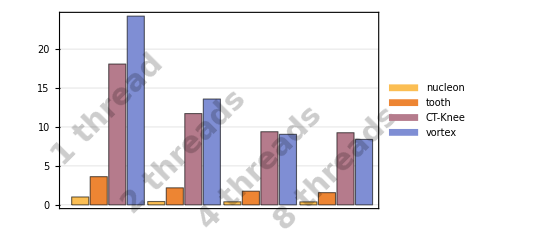

```mathematica
rotateLabel[label_]:=Style[Rotate[label,Pi/4],30,Bold,Opacity[0.2],FontFamily->"Helvetica"]
BarChart[data,ChartLegends->{"nucleon","tooth","CT-Knee","vortex"},ChartLabels->{Placed[{"1 thread","2 threads","4 threads","8 threads"},Center,rotateLabel],{"","","",""}},PlotTheme->"Detailed"]
```

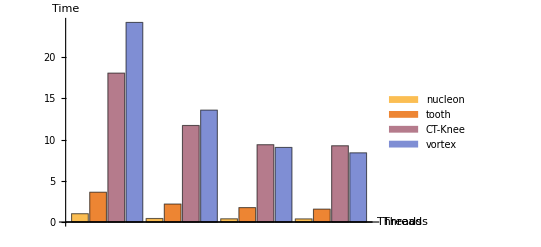

```mathematica
BarChart[data,ChartLegends->{"nucleon","tooth","CT-Knee","vortex"},AxesLabel->{"Threads","Time"},ImagePadding->{{10,40},{20,20}},PlotTheme->"Default"]
```

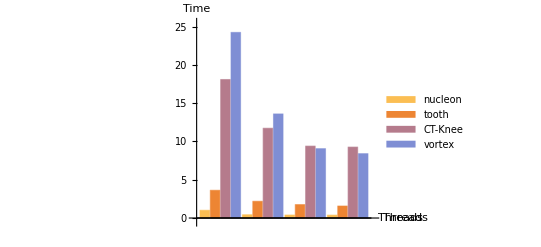

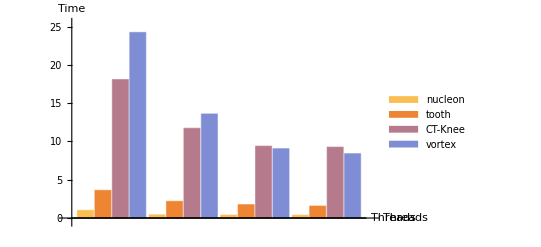

```mathematica
data2=Transpose@data
```

{{1.0101,0.425904,0.390213,0.378027},{3.61915,2.18363,1.75099,1.56567},{18.082,11.7211,9.38899,9.26095},{24.2338,13.5888,9.0546,8.40213}}

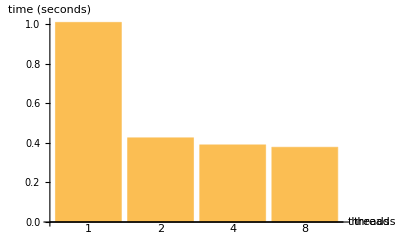
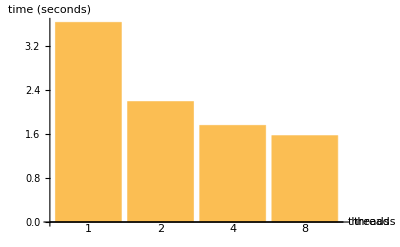
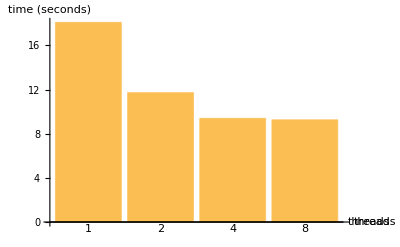
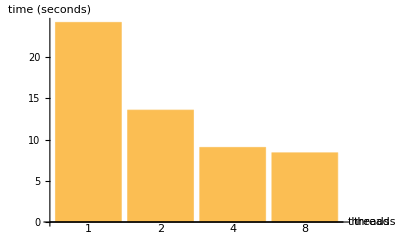

```mathematica
title={"nucleon","tooth","CT-Knee","vortex"};
charts=Table[BarChart[data2[[i]],ChartLabels->{1,2,4,8},AxesLabel->{"threads","time (seconds)"},PlotTheme->Automatic,BaseStyle->{FontSize->14}],{i,Length@data2}]
```

```mathematica
MapIndexed[Export[NotebookDirectory[]<>"~plot\\"<>title[[First@#2]]<>"_performance.pdf",#]&,charts]
```

{D:\document\work\time-varying-visualization\~plot\nucleon_performance.pdf,D:\document\work\time-varying-visualization\~plot\tooth_performance.pdf,D:\document\work\time-varying-visualization\~plot\CT-Knee_performance.pdf,D:\document\work\time-varying-visualization\~plot\vortex_performance.pdf}